```mathematica
ClearAll["Global`*"];

(*---parameters---*)
diff=1.0;
pouter=2;
pinner = 0;
uExt=1.0;
vExt=0.0;
k=0.0;
c=0.5;    (*interface position*)
rmin = 1*^-6;
R = 3;
(*---PDEs (operator form)----diff u''+k u==0-diff v''-k u==0*)
(*Left solver:integrate from x=0 to x=c with initial values u(0)=u0,v(0)=v0.Use Neumann (no-flux) at x=0 via initial derivative conditions u'[0]==0 and v'[0]==0. We'll provide values at x=0 (u0,v0) and implicit derivative zero is applied as extra conditions.*)
leftSolver=ParametricNDSolveValue[
{-diff*(u''[x] + (2/x)*u'[x])+k*u[x]==0,
-diff*(v''[x] + (2/x)*v'[x])-k*u[x]==0,
(*Neumann at x=0*)
u'[rmin]==0,
v'[rmin]==0,
(*initial values at x=0:parameters*)
u[rmin]==u0,
v[rmin]==v0},
{u,v},
{x,rmin,c},
{u0,v0}];
rightSolver=ParametricNDSolveValue[
{-diff*(u''[x] + (2/x)*u'[x])+k*u[x]==0,
-diff*(v''[x] + (2/x)*v'[x])-k*u[x]==0,
(*Robin at x=1*)
u'[R]==(pouter/diff)*(1-u[R]),
v'[R]==(pouter/diff)*(0-v[R]),
(*initial values at x=c*)
u[c]==uC,
v[c]==vC
},
{u,v},
{x,c,R},
{uC,vC}];
```

```mathematica
matchingResiduals[{u0_?NumericQ,v0_?NumericQ,alpha_?NumericQ,beta_?NumericQ}]:=Module[{left,right,uLc,vLc,duLc,dvLc,uRC,vRC,duRc,dvRc,uR1,vR1,duR1,dvR1},left=leftSolver[u0,v0];
uLc=left[[1]][c]//N;vLc=left[[2]][c]//N;
duLc=left[[1]]'[c]//N;dvLc=left[[2]]'[c]//N;
uRC=alpha uLc;
vRC=beta vLc;
right=rightSolver[uRC,vRC];
duRc=right[[1]]'[c]//N;dvRc=right[[2]]'[c]//N;
uR1=right[[1]][R]//N;vR1=right[[2]][R]//N;
duR1=right[[1]]'[R]//N;dvR1=right[[2]]'[R]//N;
(*Residuals*)
{diff*duRc-diff*duLc-pinner*(uRC-uLc),diff*dvRc-diff*dvLc-pinner*(vRC-vLc),
duR1-(pouter/diff)*(uExt-uR1),
dvR1-(pouter/diff)*(vExt-vR1)}
]
```

```mathematica
initGuess={0.2,0.5,1.4,1.8};
```

```mathematica
{0.2,0.5,1.4,1.8}
```

{0.2,0.5,1.4,1.8}

```mathematica
solMatch=FindRoot[
matchingResiduals[
{u0,v0,alpha,beta}]=={0,0,0,0},
{
{u0,initGuess[[1]]},
{v0,initGuess[[2]]},
{alpha,initGuess[[3]]},
{beta,initGuess[[4]]}
},
MaxIterations->10,
PrecisionGoal->15,
AccuracyGoal->15,
WorkingPrecision->40
]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 10 iterations.

{u0→0.704415,v0→-0.0409272,alpha→1.37577,beta→-0.926382}

```mathematica
{u0Sol,v0Sol,alphaSol,betaSol}={u0,v0,alpha,beta}/. solMatch;
```

```mathematica
Print["Solved parameters:"];
Print["u0 = ",u0Sol,", v0 = ",v0Sol,", alpha = ",alphaSol,", beta = ",betaSol];

(*---Reconstruct left/right solutions*)
leftFinal=leftSolver[u0Sol,v0Sol];
uLeftFunc=leftFinal[[1]];
vLeftFunc=leftFinal[[2]];

uRC=alphaSol*uLeftFunc[c];
vRC=betaSol*vLeftFunc[c];
rightFinal=rightSolver[uRC,vRC];
uRightFunc=rightFinal[[1]];
vRightFunc=rightFinal[[2]];

(*---Piecewise full-domain solutions*)
uSol[x_]:=Piecewise[{{uLeftFunc[x],x<=c},{uRightFunc[x],x>c}}];
vSol[x_]:=Piecewise[{{vLeftFunc[x],x<=c},{vRightFunc[x],x>c}}];

(*---Plot solutions---*)
Plot[Evaluate[{uSol[x],vSol[x]}],{x,rmin,R},PlotLegends->{"u(x)","v(x)"},AxesLabel->{"x","Concentration"},PlotTheme->"Detailed",PlotRange->All]
```

Solved parameters:

u0 = 0.704415, v0 = -0.0409272, alpha = 1.37577, beta = -0.926382

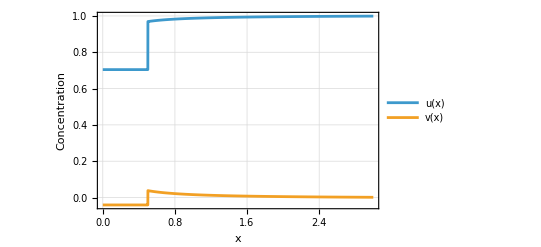

-Graphics-

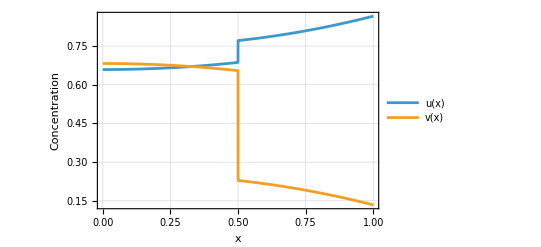

-Graphics-

```mathematica
solMatch
```

{u0→0.704415,v0→-0.0409272,alpha→1.37577,beta→-0.926382}

```mathematica
data=Table[{x,N[uSol[x]],N[vSol[x]]},{x,0,1,0.01}   (*adjust step size as needed*)];
Export["Documents/solution.csv",Prepend[data,{"x","u","v"}]];
```

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[data,{x,u,v}].

Documents/solution.csv